```mathematica
th[y_]:=ArcSin[y]
```

```mathematica
ph[x_,y_]:=ArcSin[(2th[y]+Sin[2th[y]])/Pi]
la[x_,y_]:=Pi*x/(2Cos[th[y]])
```

```mathematica
D[ph[0,y],y]//FullSimplify
```

(4 √(2-2 y^2))/(√(-1+2 π^2+Cos[4 ArcSin[y]]-8 ArcSin[y] (ArcSin[y]+Sin[2 ArcSin[y]])))

```mathematica
D[la[x,y],x]
```

π/(2 √(1-y^2))

```mathematica
%%/%//FullSimplify
```

-(8 √2 (-1+y^2))/(π √(-1+2 π^2+Cos[4 ArcSin[y]]-8 ArcSin[y] (ArcSin[y]+Sin[2 ArcSin[y]])))

```mathematica
?NSolve
```

NSolve[expr,vars] attempts to find numerical approximations to the solutions of the system expr of equations or inequalities for the variables vars. 
NSolve[expr,vars,Reals] finds solutions over the domain of real numbers.

```mathematica
?Roots
```

Roots[lhs==rhs,var] yields a disjunction of equations which represent the roots of a polynomial equation.

```mathematica
?FindRoot
```

RowBox[{"FindRoot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}]}], "]"}] searches for a numerical root of StyleBox["f", "TI"], starting from the point RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}].
RowBox[{"FindRoot", "[", RowBox[{RowBox[{StyleBox["lhs", "TI"], "==", StyleBox["rhs", "TI"]}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}]}], "]"}] searches for a numerical solution to the equation RowBox[{StyleBox["lhs", "TI"], "==", StyleBox["rhs", "TI"]}]. 
RowBox[{"FindRoot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] searches for a simultaneous numerical root of all the SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].
RowBox[{"FindRoot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["eqn", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["eqn", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] searches for a numerical solution to the simultaneous equations SubscriptBox[StyleBox["eqn", "TI"], StyleBox["i", "TI"]].

```mathematica
FindRoot[%624==Cos[ph[0,y]],{y,0.1}]
```

{y→0.540083}

```mathematica
%624/.y->-0.05390702905030595
```

0.810123

```mathematica
ph[0,0.5400827917183314]
```

0.710989

```mathematica
%633/Degree (* Mollweide *)
```

40.7367

```mathematica
(%-40)*60
```

44.1997

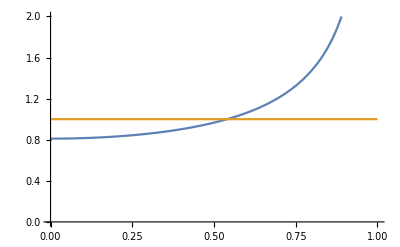

```mathematica
Plot[{%624/Cos[ph[0,y]],1},{y,0,1},PlotRange->{0,2}]
```

```mathematica
FindRoot[%624==2Cos[ph[0,y]],{y,0.1}]
```

{y→0.890043-5.77649×10^-17 ⅈ}

```mathematica
ph[0,0.8900427238041166]
```

1.27634

```mathematica
%/Degree (*Tobler*)
```

73.1288

```mathematica
(%-73)*60
```

7.73095